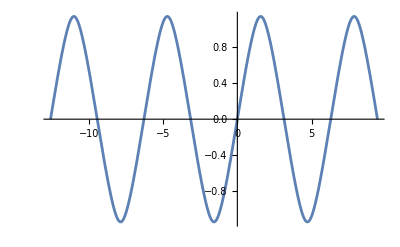

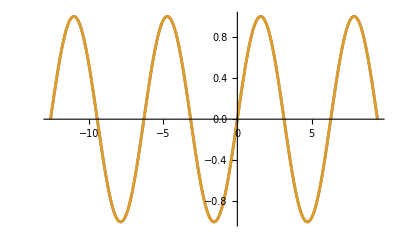

```mathematica
approx[x_]:=
Plot[approx[x], {x, -4 Pi, 3Pi}]
Plot[{Sin[x], approx[approx[x]]}, {x, -4 Pi, 3Pi}]
```

```mathematica
IntegralLoss[f_]:=NIntegrate[(Sin[x]-f[f[x]])^2, {x, -2Pi, 2Pi}]
IntegralLoss[approx]
```

1.36716×10^-19